## What’s Here

This notes shows some primary calculations on the propulsion system using only gas.

## Pre

Image size is defined

```mathematica
imgSize=500;
```

## Fundamental Physics & Mathematics

This is something like the Tsiolkovsky rocket equation.

m(d v)/(d t)=-v_e (d m)/(d t)

Next we assume that the velocity of gas in rocket frame v_e is constant.

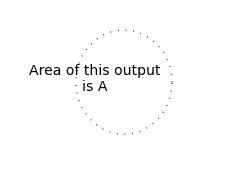

We assume the outlet of the gas is a constant area, and the density of gas at the outlet is ρ (assuming this is constant since we already assumed that the output velocity is constant). Thus we can calculate the mass leakage of the system which works as the propulsion of the equipment.

v-v_0=v_e Log[(ρ v_e A t_0-m_0)/(ρ v_e A t-m_0)]

It is good to make v_0=0, t_0=0.

v=v_e Log[m_0/(ρ v_e A t-m_0)]

Acceleration

D[v_e Log[m_0/(ρ v_e A t-m_0)],t]

-(A ρ v_e^2)/(-m_0+A t ρ v_e)

#### More Real

Now we have to determine the velocity of the gas output. A function gives us the result, that is leakage current of gas is

Q=μ A √((2Δ P)/ρ)

Here we can choose μ∈[0.60,0.62]

Q is just the product of A and v_e, Q=v_e A, i.e.,

v_e=μ √((2 Δ P)/ρ)

Substitution,

v=μ √((2(P-P_0))/(P/P_0 ρ_0))Log[m_0/(m_0-P/P_0 ρ_0 A μ √((2(P-P_0))/(P/P_0 ρ_0))t)]

ve Log[m0/(m0-ρ ve A t)]/.{ve→√2 μ √((P-P0)/(P/P0 ρ0)) ,ρ→(P ρ0)/P0}

√2 μ √(((P-P0) P0)/(P ρ0)) Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]

Before we use this expression, we need to split the m0 into two parts, one is the mass of gas, the other part is the mass of the body, volume, everything else.

m0 -> M0+m0

result is

√2 μ √(((P-P0) P0)/(P ρ0)) Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]/.{m0→(M0+m0)}

√2 μ √(((P-P0) P0)/(P ρ0)) Log[(m0+M0)/(m0+M0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]

Acceleration

D[√2 μ Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),t]

(2 A (P-P0) μ^2)/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)

## Analysis

#### Simple Examination

Now we just show the scheme of this result

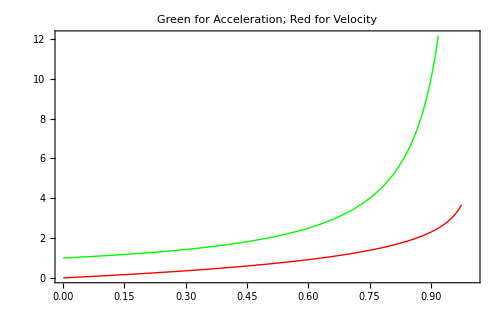

```mathematica
Show[Table[Plot[func[[1]],{t,0,1},PlotStyle->func[[2]],AxesOrigin->{0,0},Frame->True,ImageSize->imgSize],{func,{{1/(1-t),Green},{Log[1/(1-t)],Red}}}],PlotLabel->"Green for Acceleration; Red for Velocity"]
```

#### More Physics

Maybe we want to know the physics of different parameters.

```mathematica
Manipulate[Grid[{{Plot[ve Log[m0/(m0-ρ ve A t)],{t,0,m0/ρ ve A},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]},{LogPlot[ve Log[m0/(m0-ρ ve A t)],{t,0,m0/ρ ve A},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]}}],{{ve,1,"Velocity of Gas"},1,10,1},{{m0,1,"Initial Mass of Equipment"},1,10,1},{{ρ,1,"Density of Gas at Outlet"},1,50,1},{{A,1,"Area of Outlet"},1,10,1}]
```

#### Even more real

If we put every number in it,

```mathematica
Manipulate[
   "Leakage Constant:"<>ToString[μ]<>";\n"
"Constant Pressure:"<>ToString[P]<>";\n"
"Initial Mass of Gas:"<>ToString[m0]<>";\n"
"Density of Air:"<>ToString[ρ0]<>";\n"
"Area of Outlet:"<>ToString[A]<>";\n"
"Mass of Everything Else:"<>ToString[M0]<>";\n"
Grid[{{Block[{P0=101325},Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]]},{Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8]]}}],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Gas"},1,50,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.01,"Area of Outlet"},0.001,1,0.001},{{M0,50,"Mass of Everything Else"},10,100,1}]
```

## Examples

We take an example here.

Mass of equipment with everything attached including the gas: 10kg

## Draft

```mathematica
Manipulate[Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8]],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Equipment"},1,60,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.01,"Area of Outlet"},0.001,1},{{M0,50,"Mass of Everything Else"},10,100,1}]
```